```mathematica
Clear["Global`*"];
(* All in mkm *)
```

```mathematica
λ=1.55;
β=(2π)/λ;
CalcWindow=1000;
N0=255;
R=100;
```

```mathematica
GaussR[r_]:=N[Exp[-(r/R)^2]];
StepR[r_]:=Piecewise[{{1.,0≤r^2<R^2},{0,r^2≥R^2}}];
```

```mathematica
LenceSpherical[r_,f_]:=N[Exp[(I β r^2)/(2 f)]];
LenseMatrix[f_]:=Array[LenceSpherical[√(#1^2+#2^2),f]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
```

```mathematica
StartBeam=Array[GaussR[√(#1^2+#2^2)]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
```

```mathematica
NoiseWindow=200;
NoiseN=100;
Ampl=0.5;
```

```mathematica
F[x_]:=RandomFunction[WhiteNoiseProcess[],{1,2}]["ValueList"][[1,1]];
```

```mathematica
(* Ampl×F[#1+#2]×GaussR[√(#1^2+#2^2)] || RandomReal[{-Ampl,Ampl}]×GaussR[√((#1 CalcWindow/NoiseWindow)^2+(#2 CalcWindow/NoiseWindow)^2)] || 
RandomVariate[NormalDistribution[0,Ampl]] + I RandomVariate[NormalDistribution[0,Ampl]]*)
NoiseArray=Array[{{N[#1],N[#2]},RandomReal[{-Ampl,Ampl}]×GaussR[√((#1 CalcWindow/NoiseWindow)^2+(#2 CalcWindow/NoiseWindow)^2)]}&,{NoiseN,NoiseN},{{-NoiseWindow,NoiseWindow},{-NoiseWindow,NoiseWindow}}];
NoiseFunction=Interpolation[Flatten[NoiseArray,1],InterpolationOrder->{1,1}];
Noise=Array[(NoiseFunction[#1×NoiseWindow/CalcWindow,#2×NoiseWindow/CalcWindow])&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
```

```mathematica
(*NoiseBeam=StartBeam+Noise;*)
NoiseBeam=StartBeam+RotateLeft[Fourier[Noise],{(N0-1)/2,(N0-1)/2}];
NoiseBeam=StartBeam;
```

```mathematica
(*{
ListPlot3D[Abs[RotateLeft[Fourier[StartBeam],{(N0-1)/2,(N0-1)/2}]],PlotRange->All,ColorFunction->"GrayTones",ImageSize->Medium],
ListPlot3D[Abs[RotateLeft[Noise,{(N0-1)/2,(N0-1)/2}]],PlotRange->All,ColorFunction->"GrayTones",ImageSize->Medium],
ListPlot3D[Abs[RotateLeft[Fourier[NoiseBeam],{(N0-1)/2,(N0-1)/2}]],PlotRange->All,ColorFunction->"GrayTones",ImageSize->Medium]
}*)
```

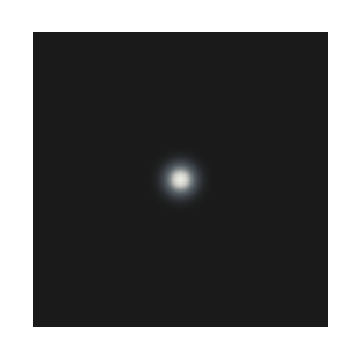
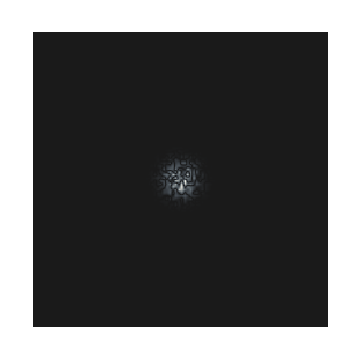
{-Graphics-,-Graphics-,-Graphics-}

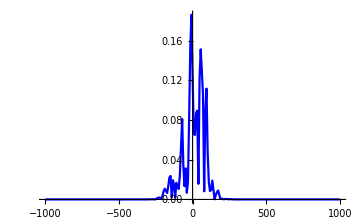
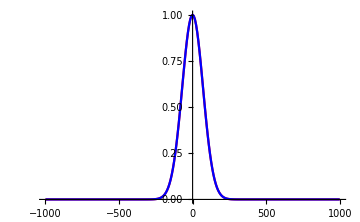

```mathematica
{
ArrayPlot[StartBeam,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],
ArrayPlot[Abs[Noise],DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],
ArrayPlot[Abs[NoiseBeam],DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]
}
{
ListPlot[Abs[Noise[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Blue],ImageSize->Medium],
Show[
ListPlot[StartBeam[[(N0+1)/2]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->All,ColorFunction->Function[{x,y},Red],ImageSize->Medium],
ListPlot[Abs[NoiseBeam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->All,ColorFunction->Function[{x,y},Blue],ImageSize->Medium]
]
}
```

```mathematica
D2Fourier=(π/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp[h_]:=Exp[I (D2Fourier h)/(2β)];
```

```mathematica
Rhole=100;
PinHoleFunction[r_]:=Piecewise[{{1.,0≤r^2<Rhole^2},{0,r^2≥Rhole^2}}];
PinHole=Array[PinHoleFunction[√(#1^2+#2^2)]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
```

```mathematica
f=5000;
```

```mathematica
LenceBeam=NoiseBeam×LenseMatrix[f];
FocusBeam=InverseFourier[FourierOp[f]×Fourier[LenceBeam ]];
FinalBeam=InverseFourier[FourierOp[f]×Fourier[FocusBeam×PinHole ]]×LenseMatrix[f];
```

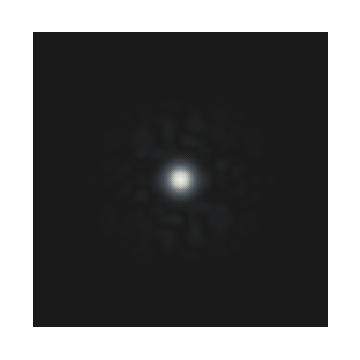
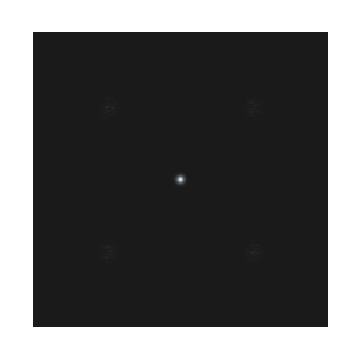
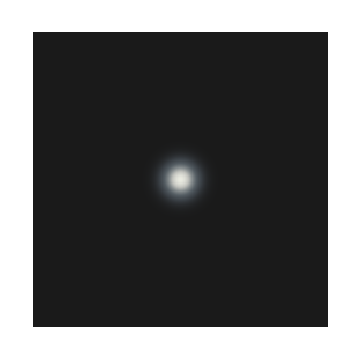

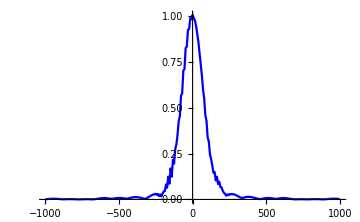
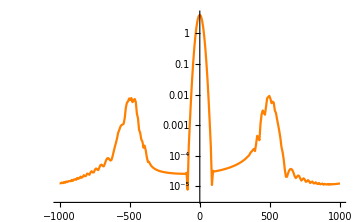
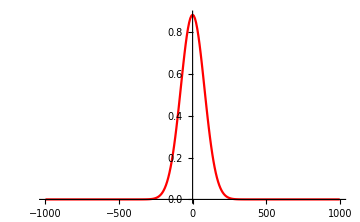

```mathematica
{
ArrayPlot[Abs[NoiseBeam],DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],ArrayPlot[Abs[FocusBeam],DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],
ArrayPlot[Abs[FinalBeam],DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]
}
{
ListPlot[Abs[NoiseBeam[[(N0+1)/2]]],
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Blue],ImageSize->Medium],
ListLogPlot[Abs[FocusBeam[[(N0+1)/2]]],
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Orange],ImageSize->Medium],
ListPlot[Abs[FinalBeam[[(N0+1)/2]]],
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Red],ImageSize->Medium]
}
```

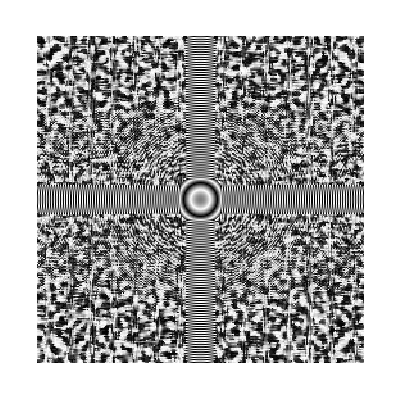

```mathematica
ArrayPlot[Arg[FocusBeam]]
```

```mathematica
(* Пучок после линзы *)
```

```mathematica
FinalBeamAfterF=InverseFourier[FourierOp[f]×Fourier[FinalBeam ]];
```

```mathematica
ListPlot[{Abs[FinalBeam[[(N0+1)/2]]]^2,Abs[FinalBeamAfterF[[(N0+1)/2]]]^2},PlotRange->All,Joined->True];
```

```mathematica
(* Фурьёвое решение *)
```

```mathematica
FourierFocusBeam=RotateLeft[Fourier[NoiseBeam],{(N0+1)/2,(N0+1)/2}];
FourierFinalBeam=Fourier[FourierFocusBeam×PinHole]×LenseMatrix[f];
```

```mathematica
{
ArrayPlot[Abs[NoiseBeam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],ArrayPlot[Abs[FourierFocusBeam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],
ArrayPlot[Abs[FourierFinalBeam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]
}
{
ListPlot[Abs[NoiseBeam[[(N0+1)/2]]]^2,
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Blue],ImageSize->Medium],
ListPlot[Abs[FourierFocusBeam[[(N0+1)/2]]]^2,
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Orange],ImageSize->Medium],
ListPlot[Abs[FourierFinalBeam[[(N0+1)/2]]]^2,
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Red],ImageSize->Medium]
}
```